## Sequence Re-Use in RB Experiments: Calculations and Plots

Select Evaluation>Evaluate Notebook to regenerate all of the figures produced by this notebook.

This notebook has many sections. We suggest enabling “Show open/close icon for control groups” in the Edit>Preference dialogue for easier navigation.

### Initialization

Functions to help us plot and export figures.

```mathematica
Needs["MaTeX`"]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
$doExport=True;
exportme[name_,opt:OptionsPattern[Export]][fig_]:=(SetDirectory[NotebookDirectory[]];
If[$doExport,
Export["../fig/"<>name<>".pdf",fig,opt];Export["../fig/"<>name<>".png",fig,opt]];fig)
```

## First Moment Tying Functions

### Weighted Cramer-Rao Bound Calculations

```mathematica
$Assumptions=α>0&&β>0&&0<μ<1&&0<t<1&&Nbin∈Integers&&Nbin≥1&&n∈Integers&&0≤n≤Nbin;
```

First we figure out the reparameterization of the Beta distribution in terms of (μ, t).

```mathematica
reparam=FullSimplify[First@Solve[{Mean[BetaDistribution[α,β]]==μ,Variance[BetaDistribution[α,β]]== t μ(1-μ)},{α,β}]]
invReparam=FullSimplify[First@Solve[{Mean[BetaDistribution[α,β]]==μ,Variance[BetaDistribution[α,β]]==t μ(1-μ)},{μ,t}]]
```

{α→(-1+1/t) μ,β→((-1+t) (-1+μ))/t}

{μ→α/(α+β),t→1/(1+α+β)}

Define the betabinomial distribution and its log-likelihood.

```mathematica
dist=BetaBinomialDistribution[α,β,Nbin];
logL=Log[PDF[dist,n]/.reparam//FullSimplify]//FunctionExpand
```

Log[1/Gamma[1+n]]+Log[Gamma[1+Nbin]]+Log[1/Gamma[1-n+Nbin]]+Log[Gamma[-1+1/t]]+Log[1/Gamma[-1+Nbin+1/t]]+Log[Gamma[-n+Nbin+((-1+t) (-1+μ))/t]]+Log[1/Gamma[((-1+t) (-1+μ))/t]]+Log[1/Gamma[(-1+1/t) μ]]+Log[Gamma[n+(-1+1/t) μ]]

Functions to compute the observed information matrix for (μ,t), and also just the μ component

```mathematica
OI[μ_,t_,Nbin_,n_]=Outer[D[logL,#1,#2]&,{μ,t},{μ,t}]//Simplify//FullSimplify;
OIμ[μ_,t_,Nbin_,n_]=OI[μ,t,Nbin,n][[1,1]]//FullSimplify;
```

Integrand of the Fisher info. Numerically, it looks like this thing is diagonal (we chose a nice parameterization), which is great because then we don’t have to invert the matrix.

```mathematica
OIpdf[μ_,t_,Nbin_,n_]=OI[μ,t,Nbin,n]PDF[dist,n]/.reparam//FullSimplify;
OIpdfμ[μ_,t_,Nbin_,n_]=OIpdf[μ,t,Nbin,n][[1,1]]//FullSimplify;
```

```mathematica
logOIpdf[μ_?NumericQ,t_,Nbin_,n_]=FunctionExpand@PowerExpand@Log@FunctionExpand@(-OIpdf[μ,t,Nbin,n]);
OIpdfNumeric[μ_,t_,Nbin_,n_]:=Exp@logOIpdf[μ,t,Nbin,n]
```

And finally the fisher information itself.

```mathematica
ClearAll@FIμ;
FIμ[μ_,t_,Nbin_?NumericQ]:=FIμ[μ,t,Nbin]=-Total[OIpdfμ[μ,t,Nbin,#]&/@Range[0,Nbin]]
```

And now a version that normalizes by the time it takes to do N_bin shots.

```mathematica
WeightedFIμ[μ_,t_,Nbin_?NumericQ,Nsamp_,tshot_,tprep_]:=(Nsamp*FIμ[μ,t,Nbin])/(Nsamp*(tprep+tshot Nbin))
```

Couldn’t get the built in minimizers to work on the integer domain for some reason, so we write a simple minimizer.

```mathematica
getMinimum[f_]:=Module[{i=1,imax=10^6,a,b},
While[f[i+1]-f[i]<0&&i≤imax,i=i*2];
a=Ceiling[i/2];b=i+2;i=Round[a+b/2];
While[
b-a>3,
If[f[i+1]-f[i]>0,b=i,a=i];i=Round[b+a]/2;
];
First@MinimalBy[Table[{x,f[x]},{x,a,b}],Last]
]
OptimalFIμ[μ_,t_,tshot_,tprep_]:=Module[{Nbin},getMinimum[1/WeightedFIμ[μ,t,#,1,tshot,tprep]&]]
```

Next we define a series of functions that compute various tradeoffs of Ntotal and Nbin.

```mathematica
FIμtradeOff[μ_,t_,Ntotal_,tradeOffRule_:Sqrt]:=Module[{Nsamp,Nbin,Nremaining},
Nbin=Ceiling[Sqrt[Ntotal]];
Nsamp=Floor[Ntotal/Nbin];
Nremaining=Ntotal-Nsamp*Nbin;
Nsamp*FIμ[μ,t,Nbin]+FIμ[μ,t,Nremaining]
]
```

```mathematica
WeightedFIμtradeOff[μ_,t_,Ntotal_,tshot_,tprep_,tradeOffRule_:Sqrt]:=Module[{Nsamp,Nbin,Nremaining},
Nbin=Ceiling[tradeOffRule[Ntotal]];
Nsamp=Floor[Ntotal/Nbin];
WeightedFIμ[μ,t,Nbin,Nsamp,tshot,tprep]
]
```

```mathematica
OptimalFIμtradeOff[μ_,t_,Ntotal_,tshot_,tprep_]:=Module[{FIμvalues},
FIμvalues=Table[WeightedFIμ[μ,t,Nbin,Floor[Ntotal/Nbin],tshot,tprep],{Nbin,1,Ntotal}];
Max[FIμvalues]
]
```

### Weighted Cramer-Rao Bound Plots

For a given set of parameters, compute datasets for different cases.

```mathematica
Module[{μ=0.5,t=0.5,tshot=100 10^-6,tprep=5000 10^-6},
xAxis=Range[1,1000];
oneDistinctDraw=Table[{Ntotal,1/FIμ[μ,t,Ntotal]},{Ntotal,xAxis}];
allDistinctDraws=Table[{Ntotal,1/(Ntotal*FIμ[μ,t,1])},{Ntotal,xAxis}];
tradeOff=Table[{Ntotal,1/FIμtradeOff[μ,t,Ntotal]},{Ntotal,xAxis}];
formula=Table[{Ntotal,μ(μ-1)/Ntotal+((Ntotal-1)/Ntotal)t μ(1-μ)},{Ntotal,xAxis}];
varianceLine=Table[((Ntotal-1)/Ntotal)t μ(1-μ),{Ntotal,xAxis}];

weightedOneDistinctDraw=Table[{Ntotal,1/WeightedFIμ[μ,t,Ntotal,1,tshot,tprep]},{Ntotal,xAxis}];
weightedAllDistinctDraws=Table[{Ntotal,1/(WeightedFIμ[μ,t,1,Ntotal,tshot,tprep])},{Ntotal,xAxis}];
weightedTradeOff=Table[{Ntotal,1/WeightedFIμtradeOff[μ,t,Ntotal,tshot,tprep]},{Ntotal,xAxis}];
weightedOptimal=Table[{Ntotal,1/OptimalFIμtradeOff[μ,t,Ntotal,tshot,tprep]},{Ntotal,xAxis}];
]
```

Now all we have to do is plot these datasets.

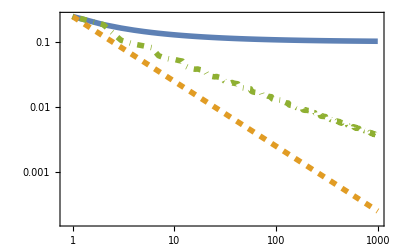

```mathematica
ListLogLogPlot[
{oneDistinctDraw,allDistinctDraws,tradeOff},
Joined->True,
PlotTheme->"Detailed",
PlotRange->All,
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashed},{Thickness[0.01],DotDashed}},
PlotLegends->Placed[
LineLegend[{MaTeX@"\\text{One distinct coin draw}",MaTeX@"\\text{All distinct coin draws}",MaTeX@"\\text{Square-root tradeoff}"},LegendFunction->Panel],
{{0.02,0.06},{0,0}}
],
FrameLabel->{MaTeX@"\\text{Total Bernoulli Trials}",MaTeX@"\\text{CRB for }q"},
ImageSize->400,
BaseStyle->texStyle,
FrameTicks->{{{10^-3,10^-2,10^-1,1},None},{Automatic,None}}
]
```

```mathematica
figLabel[str_,pos_:{1,1}]:=Inset[Framed[MaTeX["\\text{"<>str<>"}"],FrameStyle->None,Background->White,ContentPadding->False],Offset[{-1,-1},Scaled[pos]],{Right,Top}]
```

```mathematica
thickness=0.007;
imagePadding={{55,10},{40,5}};
Module[{μ=0.5,t=0.5,tshot=100 10^-6,tprep=5000 10^-6},
xAxis=Range[1,1000];
oneDistinctDraw=Table[{Ntotal,1/WeightedFIμ[μ,t,Ntotal,1,tshot,0]},{Ntotal,xAxis}];
allDistinctDraws=Table[{Ntotal,1/(WeightedFIμ[μ,t,1,Ntotal,tshot,0])},{Ntotal,xAxis}];
tradeOff=Table[{Ntotal,1/WeightedFIμtradeOff[μ,t,Ntotal,tshot,0]},{Ntotal,xAxis}];

weightedOneDistinctDraw=Table[{Ntotal,1/WeightedFIμ[μ,t,Ntotal,1,tshot,tprep]},{Ntotal,xAxis}];
weightedAllDistinctDraws=Table[{Ntotal,1/(WeightedFIμ[μ,t,1,Ntotal,tshot,tprep])},{Ntotal,xAxis}];
weightedTradeOff=Table[{Ntotal,1/WeightedFIμtradeOff[μ,t,Ntotal,tshot,tprep]},{Ntotal,xAxis}];
weightedOptimal=Table[{Ntotal,1/OptimalFIμtradeOff[μ,t,Ntotal,tshot,tprep]},{Ntotal,xAxis}];
]
dosqrt[list_]:={#1,Sqrt@#2}&@@@list
fig1=ListLogLogPlot[
dosqrt/@{oneDistinctDraw,allDistinctDraws,tradeOff},
Joined->True,
PlotTheme->"Detailed",
PlotRange->{1/350,1/3},
PlotStyle->{{Thickness[thickness]},{Thickness[thickness],Dashed},{Thickness[thickness],DotDashed}},
FrameLabel->{MaTeX@"\\text{Total Bernoulli Trials}",MaTeX@"\\sqrt{\\text{WCRB}(\\overline{q})}"},
ImageSize->350,
BaseStyle->texStyle,
FrameTicks->{{{10^-3,1/200,10^-2,1/20,10^-1,1},None},{Automatic,None}},
ImagePadding->imagePadding,
Epilog->figLabel["(a)"]
];
fig2=ListLogLogPlot[
dosqrt/@{weightedOneDistinctDraw,weightedAllDistinctDraws,weightedTradeOff,weightedOptimal},
Joined->True,
PlotTheme->"Detailed",
PlotRange->{1/350,1/3},
PlotStyle->{{Thickness[thickness]},{Thickness[thickness],Dashed},{Thickness[thickness],DotDashed},{Thickness[thickness],Dotted}},
PlotLegends->Placed[
LineLegend[{MaTeX@"\\text{One distinct coin draw}",MaTeX@"\\text{All distinct coin draws}",MaTeX@"\\text{Square-root tradeoff}",MaTeX@"\\text{Optimal Tradeoff}"}],
Automatic
],
FrameLabel->{MaTeX@"\\text{Total Bernoulli Trials}",MaTeX@"\\sqrt{\\text{WCRB}(\\overline{q})}"},
ImageSize->350,
BaseStyle->texStyle,
FrameTicks->{{{10^-3,1/200,10^-2,1/20,10^-1,1},None},{Automatic,None}},
ImagePadding->imagePadding,
Epilog->figLabel["(b)"]
];
Row[{fig1,fig2}]
```

-Graphics--Graphics-

```mathematica
Module[{μs={0.5,0.6,0.7,0.9,0.9999},t=0.5,tshot=100 10^-6,data},
data=Table[Table[{ratio,First@OptimalFIμ[μ,t,tshot,tshot*ratio]},{ratio,10^Range[0,4,0.05]}],{μ,μs}];
fig3=ListLogLogPlot[
data,
Joined->True,
PlotTheme->"Detailed",
InterpolationOrder->0,
FrameLabel->MaTeX/@{"t_\\text{pick}/t_\\text{flip}","N_\\text{optimal}"},
ImageSize->350,
ImagePadding->imagePadding,
Epilog->figLabel["(c)"],
PlotRange->{0.5,9000}
];
data=Table[Table[{ratio,Sqrt@Last@OptimalFIμ[μ,t,tshot,tshot*ratio]},{ratio,10^Range[0,4,0.05]}],{μ,μs}];
fig4=ListLogLogPlot[
data,
Joined->True,
PlotTheme->"Detailed",
PlotLegends->LineLegend[MaTeX/@Table["\\overline{q}="<>ToString[μ],{μ,μs}]],
InterpolationOrder->0,
FrameLabel->MaTeX/@{"t_\\text{pick}/t_\\text{flip}","\\text{Optimal }\\sqrt{\\text{WCRB}(\\overline{q})}"},
ImageSize->350,
FrameTicks->{{{10^-3,10^-2,10^-1,1,10},None},{Automatic,None}},
ImagePadding->imagePadding,
PlotRange->{1/10000,2},
Epilog->figLabel["(d)"]
]
];
Row[{fig3,fig4}]
```

-Graphics--Graphics-

```mathematica
exportme["betabin-crb"]@Grid[
{{
Legended[fig1,Placed[First@Last@fig2,{{0.17,1},{0,1}}]],
First@fig2
},{
Legended[fig3,Placed[First@Last@fig4,{{0.17,1},{0,1}}]],
First@fig4
}},
Alignment->{Left}]
```

-Graphics-

## Second Moment Tying Functions

### Optimal Bayes Risk for Unitarity Estimation w/ No Switching Cost

We compute the MSE for estimating the second moment of a beta-binomial distribution by summing the squares of i samples with n binomial trials each and averaging. We do so assuming a particular assignment of the (μ,μ_2) parameterization of the beta-binomial distribution. This parameterization is particularly useful in our case, as μ_2 is then the second-moment parameter that we are interested in estimating, such that the MSE of interest is 𝔼_data[((μ̂)_2-μ_2)^2]=𝔼[(μ̂)_2^2]-2𝔼[(μ̂)_2]μ_2+μ_2^2. We start by defining a few assumptions that will be useful going through.

```mathematica
$Assumptions={
n∈Integers,n>0,
i∈Integers,i>0,
μ≥0,μ≤1,
μ2≥μ^2,μ2≤μ,
T>0
}
```

{n∈Integers,n>0,i∈Integers,i>0,μ≥0,μ≤1,μ2≥μ^2,μ2≤μ,T>0}

Next, we define our reparameterization of the Beta distribution and check that its moments are what we expect.

```mathematica
μBetaParams[μ_,μ2_]:=Sequence[(μ(μ-μ2))/(μ2-μ^2),((1-μ)(μ-μ2))/(μ2-μ^2)]
```

```mathematica
Expectation[x,x\[Distributed]BetaDistribution[μBetaParams[μ,μ2]]]
```

μ

```mathematica
Expectation[x^2,x\[Distributed]BetaDistribution[μBetaParams[μ,μ2]]]
```

μ2

In order to decompose the MSE into moments as above, it is helpful to first compute the second and fourth moments of the beta-binomial distribution for this parametrization.

```mathematica
QMoment[2,μ_,μ2_,n_]=FullSimplify[Moment[BetaBinomialDistribution[μBetaParams[μ,μ2],n],2]]
```

n (μ+(-1+n) μ2)

```mathematica
QMoment[4,μ_,μ2_,n_]=FullSimplify[Moment[BetaBinomialDistribution[μBetaParams[μ,μ2],n],4]]
```

-1/((μ (-1+3 μ)-2 μ2) (μ-2 μ^2+μ2))n (μ^3-5 μ^4+6 μ^5+μ^2 (-4+7 n+(16-n (17+6 n)) μ+2 (-1+n) (9+n (4+n)) μ^2) μ2+μ (5+3 n (-5+4 n)-17 μ+n (36-n (12+7 n)) μ+3 (6-7 n+n^3) μ^2) μ2^2+(-1+n) (2+n^2 (-3+μ) (-2+μ)+6 (-1+μ) μ-n (-2+μ) (-3+5 μ)) μ2^3)

We can now compute the moments 𝔼[(μ̂)_2] and 𝔼[(μ̂)_2^2]. Note that 𝔼[(μ̂)_2]=𝔼[∑_(i=1)^I Q_i^2]/(i n^2)=∑_(j=1)^i 𝔼[Q_j^2]/(i n^2)=𝔼[Q^2]/n^2 by linearity. From the calculation in the main text, 𝔼[(μ̂)_2^2]=(1/i^2 n^4)(i 𝔼[Q^4]+i(i-1)𝔼^2[Q^2]). Thus, the mean-squared error for (μ̂)_2 is given by:

```mathematica
MSE[μ_,μ2_,n_,i_]=FullSimplify@With[{
Q2=QMoment[2,μ,μ2,n],
Q4=QMoment[4,μ,μ2,n]
},
With[{
𝔼μ2Est=Q2/n^2,
𝔼μ2Est2=(1/(i^2 n^4))(i Q4+i(i-1)Q2^2)
},
𝔼μ2Est2+μ2^2-2μ2 𝔼μ2Est
]
]
```

μ2^2-(2 μ2 (μ+(-1+n) μ2))/n+1/(i n^3)((-1+i) n (μ+(-1+n) μ2)^2-1/((μ (-1+3 μ)-2 μ2) (μ-2 μ^2+μ2))(μ^3-5 μ^4+6 μ^5+μ^2 (-4+7 n+(16-n (17+6 n)) μ+2 (-1+n) (9+n (4+n)) μ^2) μ2+μ (5+3 n (-5+4 n)-17 μ+n (36-n (12+7 n)) μ+3 (6-7 n+n^3) μ^2) μ2^2+(-1+n) (2+n^2 (-3+μ) (-2+μ)+6 (-1+μ) μ-n (-2+μ) (-3+5 μ)) μ2^3))

Next, we eliminate the dependence on the true μ and μ_2 values by considering the Bayes risk instead of the risk (MSE). That is, we take the expectation over a uniform prior on the valid set of μ and μ_2.

```mathematica
BetaBinomialUniformPrior=ProbabilityDistribution[1,{μ,0,1},{μ2,μ^2,μ}];
```

```mathematica
BayesRisk[n_,i_]=Expectation[MSE[μ,μ2,n,i],{μ,μ2}\[Distributed]BetaBinomialUniformPrior]
```

(n (-208+8 i+352 Log[2]-33 Log[3])-2 n^2 (-88+96 Log[2]-9 Log[3])+n^3 (40+32 Log[2]-3 Log[3])+2 (52-96 Log[2]+9 Log[3]))/(3360 i n^3)

Letting T=i n be constant, such that i=T/n, we can then minimize the Bayes risk for the optimal n.

```mathematica
BayesRiskNoSwitching[n_,T_]=Assuming[T>1,FullSimplify@BayesRisk[n,T/n]]
```

(8 (13-26 n+22 n^2+5 n^3+T+4 (-3+n) (-2+n) (-1+n) Log[2])-3 (-3+n) (-2+n) (-1+n) Log[3])/(3360 n^2 T)

We can then define a sensitivity by analogy to §7.1 of the main text, taking the limit as T→∞ to examine the asymptotic behavior of our n vs. i tradeoff.

```mathematica
SensitivityNoSwitching[n_]=T BayesRiskNoSwitching[n,T]//Simplify
```

(8 (13-26 n+22 n^2+5 n^3+T+4 (-3+n) (-2+n) (-1+n) Log[2])-3 (-3+n) (-2+n) (-1+n) Log[3])/(3360 n^2)

We find the optimal sequence length by setting the derivative of the sensitivity to zero and solving. In doing so, we select the first (real) root. Since the derivative is a cubic equation in T, we will get a pair of complex roots as well.

```mathematica
OptimalSequenceReuseNoSwitching[T_]=Simplify[n/.Solve[D[SensitivityNoSwitching[n],n]==0,n]⟦1⟧]
```

(-8320 3^(2/3)+7424 3^(2/3) Log[2]+11264 3^(2/3) Log[2]^2-696 3^(2/3) Log[3]-2112 3^(2/3) Log[2] Log[3]+99 3^(2/3) Log[3]^2+3^(1/3) (40+32 Log[2]-3 Log[3])^(2/3) (37440+2880 T-39168 Log[2]+2304 T Log[2]-55296 Log[2]^2+3672 Log[3]-216 T Log[3]+10368 Log[2] Log[3]-486 Log[3]^2+√(120+96 Log[2]-9 Log[3]) √(20680192-11763712 Log[2]^3+1728 T^2 (40+32 Log[2]-3 Log[3])+7450560 Log[3]+726192 Log[3]^2+9693 Log[3]^3+3072 Log[2]^2 (26896+1077 Log[3])-96 Log[2] (827840+161376 Log[3]+3231 Log[3]^2)-864 T (-2080+3072 Log[2]^2-204 Log[3]+27 Log[3]^2-64 Log[2] (-34+9 Log[3]))))^(2/3))/(3 (40+32 Log[2]-3 Log[3])^(4/3) (37440+2880 T-39168 Log[2]+2304 T Log[2]-55296 Log[2]^2+3672 Log[3]-216 T Log[3]+10368 Log[2] Log[3]-486 Log[3]^2+√(120+96 Log[2]-9 Log[3]) √(20680192-11763712 Log[2]^3+1728 T^2 (40+32 Log[2]-3 Log[3])+7450560 Log[3]+726192 Log[3]^2+9693 Log[3]^3+3072 Log[2]^2 (26896+1077 Log[3])-96 Log[2] (827840+161376 Log[3]+3231 Log[3]^2)-864 T (-2080+3072 Log[2]^2-204 Log[3]+27 Log[3]^2-64 Log[2] (-34+9 Log[3]))))^(1/3))

This is perhaps best represented as a series expanded about T=∞:

```mathematica
Series[OptimalSequenceReuseNoSwitching[T],{T,∞,0}]
```

2 (2/(40+32 Log[2]-3 Log[3]))^(1/3) T^(1/3)+((-208+352 Log[2]-33 Log[3]) (1/T)^(1/3))/(6 2^(1/3) (40+32 Log[2]-3 Log[3])^(2/3))+O[1/T]^(2/3)

```mathematica
Series[OptimalSequenceReuseNoSwitching[T],{T,∞,0}]//N
```

0.647697 T^(1/3)-0.00232827 (1/T)^(1/3)+O[1/T]^(2/3)

### Generalization to Finite Switching Cost

```mathematica
On[Assert];
```

We can now reuse much of the same machinery to generalize to the finite switching cost case, T=i(t_pick+n t_flip). For simplicity, we will proceed in the unitless parameterization τ:=t_pick/t_flip such that T/t_flip=i(τ+n). Changing t_flip while holding τ constant thus will only rescale the sensitivity, not change where the optimal sequence length occurs. We will thus take t_flip=1 (without units!) for the purposes of finding the optimal sequence length.

```mathematica
BayesRiskWSwitching[n_,T_,τ_]=Assuming[{T>0,τ>0},FullSimplify@BayesRisk[n,T/(n+τ)]]
```

((n+τ) (2 (52-96 Log[2]+9 Log[3])+n (-208+(8 T)/(n+τ)+352 Log[2]+8 n (22+5 n+4 (-6+n) Log[2])-33 Log[3]-3 (-6+n) n Log[3])))/(3360 n^3 T)

```mathematica
Assert[BayesRiskWSwitching[n,T,0]==BayesRiskNoSwitching[n,T]//Simplify]
```

```mathematica
Sensitivity[n_,T_,τ_]=Simplify[T BayesRiskWSwitching[n,T,τ]]
```

((n+τ) (2 (52-96 Log[2]+9 Log[3])+n (-208+(8 T)/(n+τ)+352 Log[2]+8 n (22+5 n+4 (-6+n) Log[2])-33 Log[3]-3 (-6+n) n Log[3])))/(3360 n^3)

```mathematica
Assert[Sensitivity[n,T,0]==SensitivityNoSwitching[n]//Simplify]
```

The expression that we obtain in this case is much less amenable to expansion as a series, so we evaluate it numerically for a few representative choices of T and τ.

```mathematica
ClearAll@OptimalSequenceReuse;
OptimalSequenceReuse[T_,τ_]:=OptimalSequenceReuse[T,τ]= Assuming[{
τ>0,T>1+τ
},
Ceiling[n/.NMinimize[{Sensitivity[n,T,τ],n>0},n,Reals]⟦2⟧]
];
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMinimize::cvdiv will be suppressed during this calculation.

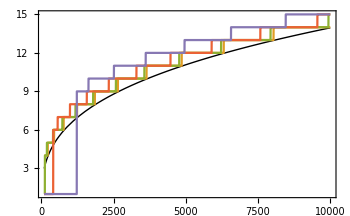

```mathematica
legendLabel[τ_]:=MaTeX["\\tau="<>ToString[τ]]
exportme["unitarity-optimal-switching-cost"]@Plot[
{
Legended[Style[OptimalSequenceReuseNoSwitching[T],Thick,Black],legendLabel[0]],
Legended[OptimalSequenceReuse[T,1],legendLabel[1]],
Legended[OptimalSequenceReuse[T,3],legendLabel[3]],
Legended[OptimalSequenceReuse[T,10],legendLabel[10]],
Legended[OptimalSequenceReuse[T,30],legendLabel[30]]
},
{T,100,10000},
FrameLabel->MaTeX/@{"\\text{Time Budget }T/t_{\\text{flip}}","\\text{Optimal Sequence Reuse }N_{\\text{opt}}"},
Frame->True,
PlotLegends->Placed[LineLegend[{},LegendLabel->MaTeX["\\text{Switching Cost Ratio }\\tau"],LegendMarkerSize->{{25,10}},LabelStyle->2],{0.75,0.35}],
PlotLabel->MaTeX@"\\text{Optimal Sequence Reuse for Second Moment Estimation}",
BaseStyle->texStyle,
ImageSize->350
]
```